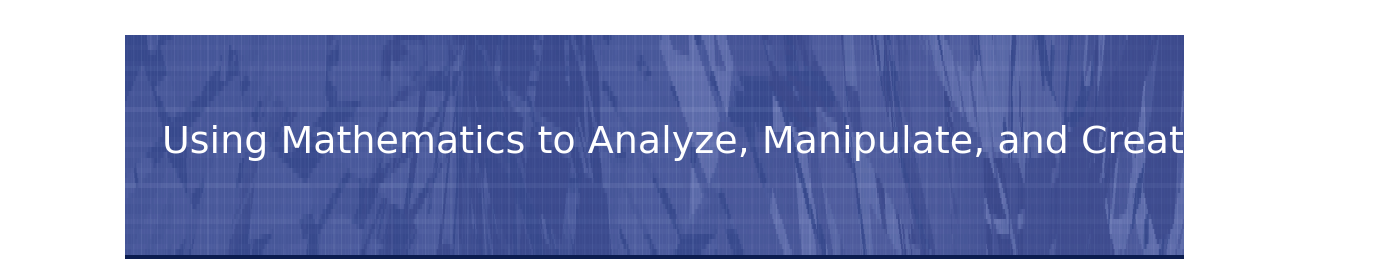
# 

## Presenters

Dirk Schlingmann, Bradley Biera, Sarah Neary, David Tran, Vivian Tran
Honors Program and College of Arts and Science
USC Upstate
dschlingmann@uscupstate.edu


"Music is an art form whose medium is sound and silence." (http://en.wikipedia.org/wiki/Music)

"Mathematics is the study of topics such as quantity (numbers), structure, space, and change." (http://en.wikipedia.org/wiki/Mathematics)

## Introduction

12 Tone Even Tempered Musical Tone System

Musical Instrument Digital Interface (MIDI)

MIDI Manufacturers Association:  www.midi.org

Importing MIDI files into Mathematica
Beethoven’s Adagio, Pathetique Sonata 2nd Movement

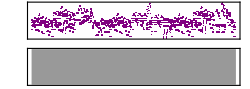

```mathematica
Clear[adagio];
adagio=Import["/Users/dschlingmann/Desktop/UpstateResearchSymposiumUsingMathematicsToAnalyzeManipulateAndCreateMusic/beethoven_pathetique2.mid"]
```

```mathematica
adagio[[1]]
```

{SoundNote[G#3,{0.,0.25},Piano,SoundVolume→0.415686],SoundNote[D#3,{0.25,0.5},Piano,SoundVolume→0.447059],SoundNote[G#3,{0.5,0.75},Piano,SoundVolume→0.486275],SoundNote[G#2,{0.,1.},Piano,SoundVolume→0.423529],SoundNote[D#3,{0.75,1.},Piano,SoundVolume→0.431373],1614,SoundNote[C3,{144.5,144.75},Piano,SoundVolume→0.376471],SoundNote[G#2,{145.,146.},Piano,SoundVolume→0.345098],SoundNote[G#1,{145.,146.},Piano,SoundVolume→0.345098],SoundNote[G#3,{145.,146.},Piano,SoundVolume→0.329412],SoundNote[C3,{145.,146.},Piano,SoundVolume→0.329412]}
 |  |  |  |

### Statistical Analysis of MIDI files

Initialization

```mathematica
Clear[stringToInt];
stringToInt[s_]:=Which[
(*
s=="C0",12,
s=="C#0",13,
s=="Db0",13,
s=="D0",14,
s=="D#0",15,
s=="Eb0",15,
s=="E0",16,
s=="F0",17,
s=="F#0",18,
s=="Gb0",18,
s=="G0",19,
s=="G#0",20,
s=="Ab0",20,
*)
s=="A0",21,
s=="A#0",22,
s=="Bb0",22,
s=="B0",23,

s=="C1",24,
s=="C#1",25,
s=="Db1",25,
s=="D1",26,
s=="D#1",27,
s=="Eb1",27,
s=="E1",28,
s=="F1",29,
s=="F#1",30,
s=="Gb1",30,
s=="G1",31,
s=="G#1",32,
s=="Ab1",32,
s=="A1",33,
s=="A#1",34,
s=="Bb1",34,
s=="B1",35,

s=="C2",36,
s=="C#2",37,
s=="Db2",37,
s=="D2",38,
s=="D#2",39,
s=="Eb2",39,
s=="E2",40,
s=="F2",41,
s=="F#2",42,
s=="Gb2",42,
s=="G2",43,
s=="G#2",44,
s=="Ab2",44,
s=="A2",45,
s=="A#2",46,
s=="Bb2",46,
s=="B2",47,

s=="C3",48,
s=="C#3",49,
s=="Db3",49,
s=="D3",50,
s=="D#3",51,
s=="Eb3",51,
s=="E3",52,
s=="F3",53,
s=="F#3",54,
s=="Gb3",54,
s=="G3",55,
s=="G#3",56,
s=="Ab3",56,
s=="A3",57,
s=="A#3",58,
s=="Bb3",58,
s=="B3",59,

s=="C4",60,
s=="C#4",61,
s=="Db4",61,
s=="D4",62,
s=="D#4",63,
s=="Eb4",63,
s=="E4",64,
s=="F4",65,
s=="F#4",66,
s=="Gb4",66,
s=="G4",67,
s=="G#4",68,
s=="Ab4",68,
s=="A4",69,
s=="A#4",70,
s=="Bb4",70,
s=="B4",71,

s=="C5",72,
s=="C#5",73,
s=="Db5",73,
s=="D5",74,
s=="D#5",75,
s=="Eb5",75,
s=="E5",76,
s=="F5",77,
s=="F#5",78,
s=="Gb5",78,
s=="G5",79,
s=="G#5",80,
s=="Ab5",80,
s=="A5",81,
s=="A#5",82,
s=="Bb5",82,
s=="B5",83,

s=="C6",84,
s=="C#6",85,
s=="Db6",85,
s=="D6",86,
s=="D#6",87,
s=="Eb6",87,
s=="E6",88,
s=="F6",89,
s=="F#6",90,
s=="Gb6",90,
s=="G6",91,
s=="G#6",92,
s=="Ab6",92,
s=="A6",93,
s=="A#6",94,
s=="Bb6",94,
s=="B6",95,

s=="C7",96,
s=="C#7",97,
s=="Db7",97,
s=="D7",98,
s=="D#7",99,
s=="Eb7",99,
s=="E7",100,
s=="F7",101,
s=="F#7",102,
s=="Gb7",102,
s=="G7",103,
s=="G#7",104,
s=="Ab7",104,
s=="A7",105,
s=="A#7",106,
s=="Bb7",106,
s=="B7",107,

s=="C8",108
(*,
s=="C#8",109,
s=="Db8",109,
s=="D8",110,
s=="D#8",111,
s=="Eb8",111,
s=="E8",112,
s=="F8",113,
s=="F#8",114,
s=="Gb8",114,
s=="G8",115,
s=="G#8",116,
s=="Ab8",116,
s=="A8",117,
s=="A#8",118,
s=="Bb8",118,
s=="B8",119*)
]
```

Statistical Analysis of Beethoven’s Adagio

```mathematica
Clear[data];
data=Table[{adagio[[1,i,1]],adagio[[1,i,2]],adagio[[1,i,3]],adagio[[1,i,4,2]]},{i,1,Length[adagio[[1]]]}]
```

{{G#3,{0.,0.25},Piano,0.415686},{D#3,{0.25,0.5},Piano,0.447059},{G#3,{0.5,0.75},Piano,0.486275},{G#2,{0.,1.},Piano,0.423529},{D#3,{0.75,1.},Piano,0.431373},{C4,{0.,1.},Piano,0.415686},1612,{D#3,{144.5,144.75},Piano,0.376471},{C3,{144.5,144.75},Piano,0.376471},{G#2,{145.,146.},Piano,0.345098},{G#1,{145.,146.},Piano,0.345098},{G#3,{145.,146.},Piano,0.329412},{C3,{145.,146.},Piano,0.329412}}
 |  |  |  |

```mathematica
Clear[dataTones];
dataTones=Table[adagio[[1,i,1]],{i,1,Length[adagio[[1]]]}]
```

{G#3,D#3,G#3,G#2,D#3,C4,G3,D#3,G3,C#3,D#3,A#3,G#3,D#3,G#3,C3,D#3,A#3,D#3,D#4,A#3,G2,C#4,D#3,G#3,G#2,D#3,C4,A#3,G2,D#3,D#4,C4,F2,G#3,G#4,D4,F3,A#4,G#3,G3,A#3,G3,D#3,A#3,G3,A#3,D#4,G3,D#2,A#3,E4,G3,A#3,G3,F4,C#2,A#3,G3,D#3,G3,A#3,C4,C#3,D#3,C#4,G#3,D#3,G#3,C3,D#3,D#4,D#3,C3,D#3,F2,C3,A3,F3,C#3,F3,C#4,A#1,C#3,C4,C#3,A#3,C#3,G#3,C#3,G3,D#2,C#3,C#3,G#1,D#3,C#3,A#3,G3,D#3,G#2,G#3,C3,D#3,G#3,G#1,C4,D#4,G#4,G#3,C4,D#3,D#4,G#3,C4,D#3,G#2,D#4,C5,G3,A#3,D#3,D#4,G3,A#3,D#3,C#3,D#4,A#4,G#3,D#4,D#3,G#4,G#3,D#4,D#3,C3,G#4,G3,D#4,D#3,A#4,D#5,D#4,G3,G2,C#5,D#3,A#4,G#3,D#4,D#3,G#2,G#4,C5,G3,D#4,D#3,G2,A#4,D#5,F3,G#4,G#2,F2,C5,G#5,F3,G#4,F2,A#5,G#2,D5,D#2,G4,G2,A#4,A#2,G4,D#3,A#4,G3,G4,A#3,A#4,D#5,G3,G4,A#3,A#4,E5,G4,C#2,G2,A#4,A#2,G4,F5,C#3,A#4,G3,G4,A#3,D#4,G3,G4,A#4,C5,C#3,C#5,D#4,C3,G#4,D#3,D#4,C3,G#4,D#3,C3,D#4,D#5,C3,D#4,F3,C4,C3,D#4,F3,F2,C4,A4,C#3,F4,F3,C#4,C#3,F4,F3,A#2,C#4,C#5,C5,A#2,C#4,A#4,D#3,C#4,G#4,A#2,C#4,G4,D#2,D#3,C#4,C#4,D#3,D#4,G3,C#4,D#3,D#4,A#4,C4,G#4,G#3,G#2,C4,C4,C4,C4,C4,C5,C4,G#5,C4,G5,F5,C4,C4,G3,E3,C4,G3,E3,C4,G3,E3,C4,G3,E3,C4,G#3,F3,C6,G#3,F3,G#5,G#3,F3,G5,F5,G#3,F3,E4,A#3,G3,E4,A#3,G3,E4,A#3,G3,E4,A#3,G3,F4,C4,G#3,C5,F4,C4,G#3,G#5,F4,C4,G#3,G5,F5,F4,C4,G#3,G#4,F4,A#3,G#4,F4,A#3,D#5,G#4,F4,A#3,G#4,F4,A#3,G#4,F4,B3,G#4,F4,B3,D5,G#4,D4,B3,F5,D#5,G#4,D4,B3,G4,D#4,C4,G4,D#4,C4,G4,D#4,C4,G4,D#4,C4,D#5,D#4,G#3,D#4,G#3,D#4,G#3,F4,G#4,B4,C5,D5,D#4,G#3,C5,A#4,G4,D#4,A#3,G4,D#4,A#3,G5,F5,G4,D#4,A#3,D#5,D5,C5,A#4,G#3,D3,A#2,A4,C5,G#3,D3,A#2,A#4,G#4,F4,G#3,D3,A#2,G3,D#3,G3,A#3,G3,A#3,G3,D#3,D#3,G#3,F3,D3,D3,G#3,F3,C3,C3,G#3,F3,B2,B2,G#3,F3,A#2,A#1,D#2,G3,D#3,A#2,A#2,G2,A#2,G2,A#3,D#2,D#4,D#4,D4,D4,G#3,F3,C4,A#1,C4,B3,B3,G#3,F3,A#3,A#2,F3,E3,E3,D#3,D#3,D3,D3,D#3,D#3,E3,E3,D#3,D#3,D3,D3,G3,C#3,D#2,G#3,C3,D#3,G#3,G#2,G#1,D#3,C4,G3,D#3,G3,C#3,D#3,A#3,G#3,D#3,G#3,C3,D#3,A#3,D#3,D#4,A#3,G2,C#4,D#3,G#3,G#2,D#3,C4,A#3,G2,D#3,D#4,C4,F2,G#3,G#4,D4,A#4,F3,G#3,G3,A#3,G3,D#3,A#3,G3,A#3,D#4,G3,D#2,A#3,E4,G3,A#3,G3,F4,C#2,A#3,G3,D#3,G3,A#3,C4,C#3,D#3,C#4,G#3,D#3,G#3,C3,D#3,D#4,D#3,C3,D#3,F2,C3,A3,F3,C#3,F3,C#4,A#1,C#3,C4,C#3,A#3,C#3,G#3,C#3,G3,D#2,C#3,C#3,G#1,D#3,C#3,G#2,D#3,A#3,G3,C3,G#3,G#1,D#4,D#4,B3,D#4,B3,D#4,B3,G#4,D#4,B3,D#4,B3,G#3,G#2,D#4,B3,B4,D#4,B3,D#4,B3,D#4,B3,A#4,D#4,B3,D#4,B3,G#4,D#4,B3,D#4,C#4,D#4,C#4,D#4,C#4,G4,D#4,C#4,A#3,A#3,D#4,C#4,C#5,A3,D#4,C#4,A#3,D#4,C#4,A#3,D#4,C#4,G#3,D#4,C#4,G3,D#4,C#4,F3,D#4,C#4,D#3,D#4,C#4,D#4,B3,D#4,B3,G#3,D#4,B3,G#4,D#4,B3,D#4,B3,D#4,B3,B4,D#4,B3,D#4,B3,D#4,B3,A#4,D#4,B3,D#4,B3,G#4,D#4,B3,D#4,A#3,D#4,A#3,D#4,A#3,G#4,D#4,A#3,D#3,D#3,D#4,A#3,G4,D3,D#4,A#3,D#3,D#4,A#3,G3,E3,D#4,A#3,G3,D#3,D#4,A#3,G3,C#3,D#4,A#3,G3,B2,D#4,A#3,G3,A#2,D#4,A#3,G3,D#4,B3,D#4,B3,G#2,D#4,B3,G#4,D#4,B3,D#4,B3,D#4,B3,B4,D#4,B3,D#4,B3,D#4,B3,A#4,D#4,B3,D#4,B3,G#4,D#4,B3,F#3,D#3,B2,A2,F#3,D#3,B2,A2,F#3,D#3,B2,A2,F#4,F#3,D#3,B2,A2,F#5,D#5,F#3,D#3,B2,A2,B4,F#3,D#3,B2,A2,G#3,E3,B2,G#2,G#3,E3,B2,G#2,G#3,E3,B2,G#2,B4,G#3,E3,B2,G#2,B5,G#5,G#3,E3,B2,G#2,E5,G#3,E3,B2,G#2,A#3,F#3,E3,C#3,A#3,F#3,E3,C#3,A#3,F#3,E3,C#3,E5,A#3,F#3,E3,C#3,E6,C#6,A#3,F#3,E3,C#3,A#5,A#3,F#3,E3,C#3,B3,G#3,E3,B2,B5,B4,B3,G#3,E3,B2,B3,G#3,E3,B2,B2,B1,D#4,B3,A3,F#3,B2,B1,B2,B1,E4,B3,G#3,B3,G#3,E3,E2,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,B3,G#3,E4,B3,G#3,B3,G#3,E3,E2,B3,G#3,G#4,B3,G#3,B3,G#3,B3,G#3,F#4,B3,G#3,B3,G#3,E4,B3,G#3,B3,A3,B3,A3,B3,A3,D#4,B3,A3,F#3,F#3,B3,A3,A4,F3,B3,A3,F#3,B3,A3,F#3,B3,A3,E3,B3,A3,D#3,B3,A3,C#3,B3,A3,B2,B3,A3,B3,G#3,B3,G#3,E3,B3,G#3,E4,B3,G#3,B3,G#3,B3,G#3,G#4,B3,G#3,B3,G#3,B3,G#3,F#4,B3,G#3,B3,G#3,E4,B3,G#3,B3,G#3,D3,F1,B3,G#3,D3,G#1,B3,G#3,D3,B1,B3,G#3,D3,D2,B3,G#3,D3,F2,B3,G#3,D3,B3,G#3,D3,G#2,B3,G#3,D3,B3,G#3,D3,D4,B3,G#3,D3,B3,G#3,D3,D4,B3,G#3,D3,B3,G#3,D3,F1,B3,G#3,D3,G#1,B3,G#3,D3,B1,B3,G#3,D3,D2,B3,G#3,D3,F2,B3,G#3,D3,B3,G#3,D3,G#2,B3,G#3,D3,B3,G#3,D3,D4,B3,G#3,D3,B3,G#3,D3,D4,B3,G#3,D3,A#3,G#3,C#3,E2,A#3,G#3,C#3,G#2,A#3,G#3,C#3,A#3,G#3,C#3,A#2,A#3,G#3,C#3,A#3,G#3,C#3,A#3,G3,C#3,D#2,A#3,G3,C#3,G2,A#3,G3,C#3,C#4,A#3,G3,D#3,C#3,A#2,A#3,G3,D#3,C#3,C#4,A#3,G3,D#3,C#3,C3,D#3,D#3,G#3,D#3,G#2,G#1,D#3,C4,G3,D#3,D#3,G3,D#3,C#3,D#3,A#3,G#3,D#3,D#3,G#3,D#3,C3,D#3,A#3,D#3,D#3,D#4,A#3,D#3,G2,C#4,D#3,G#3,D#3,G#2,D#3,C4,A#3,D#3,G2,D#3,D#4,C4,G#3,F2,G#3,G#4,D4,A#4,G#3,F3,G#3,G3,A#3,A#3,G3,A#3,D#3,A#3,G3,A#3,A#3,D#4,G3,A#3,D#2,A#3,E4,G3,A#3,A#3,G3,A#3,F4,C#2,A#3,G3,D#3,D#3,G3,A#3,D#3,C4,C#3,D#3,C#4,G#3,D#3,D#3,G#3,D#3,C3,D#3,D#4,D#3,C3,C3,D#3,C3,F2,C3,A3,F3,C#3,C#3,F3,C#3,C#4,A#1,C#3,G3,C#4,C#3,C4,C#3,A#3,C#3,A#3,C#3,G#3,D#2,C#3,G3,C#3,D#3,G#1,D#3,C#3,D#3,A#3,G3,G#2,D#3,C3,D#3,G#3,G#3,G#1,C4,D#4,G#4,G#3,C4,D#3,D#4,D#3,D#4,G#3,C4,D#3,D#4,G#2,C5,D#3,D#4,G3,A#3,D#3,D#4,D#3,D#4,G3,A#3,C#3,A#4,D#3,D#4,D#3,D#4,G#3,D#4,D#3,G#4,D#3,G#4,G#3,D#4,D#3,G#4,C3,D#3,G#4,G3,D#4,D#3,A#4,D#5,D#3,A#4,G3,D#4,D#3,A#4,C#5,G2,D#3,A#4,G#3,D#4,D#3,G#4,G#2,C5,D#3,G#4,G3,D#4,D#3,A#4,G2,D#5,D#3,A#4,F3,G#4,G#2,C5,F2,G#5,G#2,C5,F3,G#4,F2,A#5,G#2,D5,G#2,D5,D#2,G4,G2,A#4,A#2,A#4,D#3,G4,G3,A#4,A#3,A#4,G4,A#4,D#5,A#4,G4,A#4,E5,D#4,A#4,C#2,G4,G2,A#4,A#2,A#4,C#3,G4,G3,A#4,F5,A#3,A#4,G4,D#4,D#4,A#4,G4,D#4,C5,D#4,C#5,C#4,G#4,D#4,D#4,G#4,D#4,D#5,C4,D#4,D#4,C4,C4,D#4,C4,A4,F3,C4,F4,C#4,C#4,F4,C#4,C#5,A#2,C#4,A#2,G4,C#5,C#4,C5,D#3,D#3,D#2,C#4,A#4,D#2,C#4,A#4,C#4,G#4,D#3,D#3,D#2,C#4,G4,G#2,D#3,D#3,C4,G#4,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#5,D#3,E5,D#3,C#3,D#2,D#3,C#3,D#2,D#3,C#3,D#2,D#3,C#3,D#2,F5,D#5,D#3,C#3,D#2,C#5,D#3,C#3,D#2,C5,D#3,C#3,D#2,A#4,D#3,C#3,D#2,G#4,D#3,C#3,D#2,D#3,C#3,D#2,G4,D#3,C#3,D#2,C#5,G4,D#3,C#3,D#2,D#3,C3,G#2,D#3,G#4,D#3,C5,D#3,D#3,D#4,D#3,D#3,D#3,D#3,D#3,D#3,D#6,D#5,E6,E5,D#3,D#3,C#3,D#2,D#3,C#3,D#2,D#3,C#3,D#2,D#3,C#3,D#2,F6,F5,D#6,D#5,D#3,C#3,D#2,C#6,C#5,D#3,C#3,D#2,C6,C5,D#3,C#3,D#2,A#5,A#4,D#3,C#3,D#2,G#5,G#4,D#3,C#3,D#2,D#3,C#3,D#2,G5,G4,D#3,C#3,D#2,C#6,C#5,G5,G4,D#3,C#3,D#2,D#3,C3,G#2,G#5,G#4,D#5,C#5,C5,C#5,F5,D#5,C#5,G4,D#4,G#4,G#3,C5,C5,A#4,A4,A#4,C#5,C5,A#4,C#4,D#3,G4,C4,G#3,G#4,C4,A#3,A3,A#3,C#4,C4,G3,A#3,C#3,D#2,C3,G#2,G#3,G#1,G#3,D#3,C3,G#2,G#1,G#3,C3}

```mathematica
Sort[dataTones]
```

{A#1,A#1,A#1,A#1,A#1,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A#2,A2,A2,A2,A2,A2,A2,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A#3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A3,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A#4,A4,A4,A4,A4,A4,A#5,A#5,A#5,A#5,B1,B1,B1,B1,B1,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B2,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B3,B4,B4,B4,B4,B4,B4,B4,B5,B5,C#2,C#2,C#2,C#2,C#2,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C#3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C3,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C#4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C4,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C#5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C5,C#6,C#6,C#6,C6,C6,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D#2,D2,D2,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D#3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D3,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D#4,D4,D4,D4,D4,D4,D4,D4,D4,D4,D4,D4,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D#5,D5,D5,D5,D5,D5,D5,D#6,D#6,E2,E2,E2,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E3,E4,E4,E4,E4,E4,E4,E4,E4,E4,E4,E4,E4,E5,E5,E5,E5,E5,E5,E6,E6,F1,F1,F2,F2,F2,F2,F2,F2,F2,F2,F2,F2,F2,F2,F2,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F#3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F3,F#4,F#4,F#4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F4,F#5,F5,F5,F5,F5,F5,F5,F5,F5,F5,F5,F6,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#1,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G#2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G2,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G#3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G3,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G#4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G4,G#5,G#5,G#5,G#5,G#5,G#5,G#5,G#5,G5,G5,G5,G5,G5,G5}

```mathematica
Union[dataTones]
```

{A#1,A#2,A2,A#3,A3,A#4,A4,A#5,B1,B2,B3,B4,B5,C#2,C#3,C3,C#4,C4,C#5,C5,C#6,C6,D#2,D2,D#3,D3,D#4,D4,D#5,D5,D#6,E2,E3,E4,E5,E6,F1,F2,F#3,F3,F#4,F4,F#5,F5,F6,G#1,G#2,G2,G#3,G3,G#4,G4,G#5,G5}

```mathematica
Table[{Count[dataTones,Union[dataTones][[i]]],Union[dataTones][[i]]},{i,1,Length[Union[dataTones]]}]
```

{{5,A#1},{20,A#2},{6,A2},{107,A#3},{18,A3},{49,A#4},{5,A4},{4,A#5},{5,B1},{22,B2},{118,B3},{7,B4},{2,B5},{5,C#2},{86,C#3},{33,C3},{44,C#4},{56,C4},{16,C#5},{24,C5},{3,C#6},{2,C6},{41,D#2},{2,D2},{192,D#3},{34,D3},{135,D#4},{11,D4},{19,D#5},{6,D5},{2,D#6},{3,E2},{28,E3},{12,E4},{6,E5},{2,E6},{2,F1},{13,F2},{17,F#3},{31,F3},{3,F#4},{19,F4},{1,F#5},{10,F5},{1,F6},{12,G#1},{36,G#2},{17,G2},{151,G#3},{82,G3},{51,G#4},{34,G4},{8,G#5},{6,G5}}

```mathematica
Clear[d];
d=Sort[Table[{Count[dataTones,Union[dataTones][[i]]],Union[dataTones][[i]]},{i,1,Length[Union[dataTones]]}]]
```

{{1,F#5},{1,F6},{2,B5},{2,C6},{2,D2},{2,D#6},{2,E6},{2,F1},{3,C#6},{3,E2},{3,F#4},{4,A#5},{5,A#1},{5,A4},{5,B1},{5,C#2},{6,A2},{6,D5},{6,E5},{6,G5},{7,B4},{8,G#5},{10,F5},{11,D4},{12,E4},{12,G#1},{13,F2},{16,C#5},{17,F#3},{17,G2},{18,A3},{19,D#5},{19,F4},{20,A#2},{22,B2},{24,C5},{28,E3},{31,F3},{33,C3},{34,D3},{34,G4},{36,G#2},{41,D#2},{44,C#4},{49,A#4},{51,G#4},{56,C4},{82,G3},{86,C#3},{107,A#3},{118,B3},{135,D#4},{151,G#3},{192,D#3}}

```mathematica
Clear[sd];
sd=Sort[Table[{stringToInt[d[[i,2]]],d[[i,1]]},{i,1,Length[d]}]]
```

{{29,2},{32,12},{34,5},{35,5},{37,5},{38,2},{39,41},{40,3},{41,13},{43,17},{44,36},{45,6},{46,20},{47,22},{48,33},{49,86},{50,34},{51,192},{52,28},{53,31},{54,17},{55,82},{56,151},{57,18},{58,107},{59,118},{60,56},{61,44},{62,11},{63,135},{64,12},{65,19},{66,3},{67,34},{68,51},{69,5},{70,49},{71,7},{72,24},{73,16},{74,6},{75,19},{76,6},{77,10},{78,1},{79,6},{80,8},{82,4},{83,2},{84,2},{85,3},{87,2},{88,2},{89,1}}

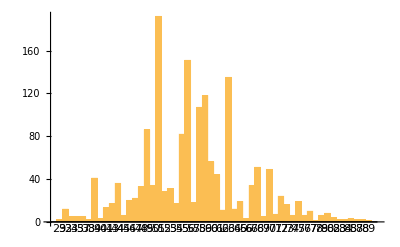

```mathematica
Clear[adagioBarChart];
adagioBarChart=BarChart[Table[sd[[i,2]],{i,1,Length[sd]}],ChartLabels->Table[sd[[i,1]],{i,1,Length[sd]}]]
```

```mathematica
Clear[dataMIDITones];
dataMIDITones=Sort[Table[stringToInt[adagio[[1,i,1]]],{i,1,Length[adagio[[1]]]}]]
```

{29,29,32,32,32,32,32,32,32,32,32,32,32,32,34,34,34,34,34,35,35,35,35,35,37,37,37,37,37,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,62,62,62,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,76,76,77,77,77,77,77,77,77,77,77,77,78,79,79,79,79,79,79,80,80,80,80,80,80,80,80,82,82,82,82,83,83,84,84,85,85,85,87,87,88,88,89}

```mathematica
Clear[median];
median=Median[dataMIDITones]
```

56

```mathematica
Clear[mean];
mean=N[Mean[dataMIDITones]]
```

56.8319

```mathematica
Clear[standardDeviation];
standardDeviation=N[StandardDeviation[dataMIDITones]]
```

9.29496

### Manipulation of MIDI files

Playing the Adagio backwards

{{C3,{0.,1.},Piano,SoundVolume→0.329412},{G#3,{0.,1.},Piano,SoundVolume→0.329412},{G#1,{0.,1.},Piano,SoundVolume→0.345098},{G#2,{0.,1.},Piano,SoundVolume→0.345098},{C3,{1.25,1.5},Piano,SoundVolume→0.376471},1614,{D#3,{145.,145.25},Piano,SoundVolume→0.431373},{G#2,{145.,146.},Piano,SoundVolume→0.423529},{G#3,{145.25,145.5},Piano,SoundVolume→0.486275},{D#3,{145.5,145.75},Piano,SoundVolume→0.447059},{G#3,{145.75,146.},Piano,SoundVolume→0.415686}}
 |  |  |  |

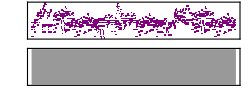

```mathematica
Clear[databw,songLength,oigada];
songLength=adagio[[1,Length[adagio[[1]]],2,2]];
databw=
Table[
{
adagio[[1,Length[adagio[[1]]]+1-i,1]],
{songLength-adagio[[1,Length[adagio[[1]]]+1-i,2,2]],
songLength-adagio[[1,Length[adagio[[1]]]+1-i,2,1]]
},
adagio[[1,Length[adagio[[1]]]+1-i,3]],
adagio[[1,Length[adagio[[1]]]+1-i,4]]
},
{i,1,Length[adagio[[1]]]}
]
oigada=Sound[SoundNote[#[[1]],#[[2]],#[[3]],#[[4]]]&/@databw]
```

Playing the Adagio reflected

{{-4,{0.,0.25},Piano,0.415686},{1,{0.25,0.5},Piano,0.447059},{-4,{0.5,0.75},Piano,0.486275},{8,{0.,1.},Piano,0.423529},{1,{0.75,1.},Piano,0.431373},{-8,{0.,1.},Piano,0.415686},{-3,{1.,1.25},Piano,0.470588},1611,{1,{144.5,144.75},Piano,0.376471},{4,{144.5,144.75},Piano,0.376471},{8,{145.,146.},Piano,0.345098},{20,{145.,146.},Piano,0.345098},{-4,{145.,146.},Piano,0.329412},{4,{145.,146.},Piano,0.329412}}
 |  |  |  |

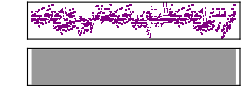

```mathematica
Clear[datarefl, center];
center=56;
refl[n_]:=center+(center-n);
datarefl=Table[{refl[stringToInt[adagio[[1,i,1]]]]-60,adagio[[1,i,2]],adagio[[1,i,3]],adagio[[1,i,4,2]]},{i,1,Length[adagio[[1]]]}]
Clear[adagiorefl];
adagiorefl=Sound[SoundNote[#[[1]],#[[2]],#[[3]],SoundVolume->#[[4]]]&/@datarefl]
```

Playing the Adagio backwards and reflected

{{4,{0.,1.},Piano,SoundVolume→0.329412},{-4,{0.,1.},Piano,SoundVolume→0.329412},{20,{0.,1.},Piano,SoundVolume→0.345098},{8,{0.,1.},Piano,SoundVolume→0.345098},{4,{1.25,1.5},Piano,SoundVolume→0.376471},{1,{1.25,1.5},Piano,SoundVolume→0.376471},1613,{1,{145.,145.25},Piano,SoundVolume→0.431373},{8,{145.,146.},Piano,SoundVolume→0.423529},{-4,{145.25,145.5},Piano,SoundVolume→0.486275},{1,{145.5,145.75},Piano,SoundVolume→0.447059},{-4,{145.75,146.},Piano,SoundVolume→0.415686}}
 |  |  |  |

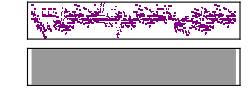

```mathematica
Clear[databwrefl,songLength,adagiobwrefl];
songLength=adagio[[1,Length[adagio[[1]]],2,2]];
databwrefl=
Table[
{
refl[stringToInt[adagio[[1,Length[adagio[[1]]]+1-i,1]]]]-60,
{songLength-adagio[[1,Length[adagio[[1]]]+1-i,2,2]],
songLength-adagio[[1,Length[adagio[[1]]]+1-i,2,1]]
},
adagio[[1,Length[adagio[[1]]]+1-i,3]],
adagio[[1,Length[adagio[[1]]]+1-i,4]]
},
{i,1,Length[adagio[[1]]]}
]
adagiobwrefl=Sound[SoundNote[#[[1]],#[[2]],#[[3]],#[[4]]]&/@databwrefl]
```

### Creation of MIDI files

Play MIDI files created by students stored in iTunes

Using famous integer sequences, Fibonnaci Numbers

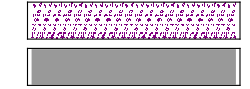

```mathematica
Clear[tonesFib,dataInstrument1,instrument1];
tonesFib=Table[Mod[Fibonacci[i],88]-39,{i,1,1200}];
dataInstrument1=Table[{tonesFib[[i]],1/10,1,1},{i,1,1200}];
instrument1=Sound[{SoundNote[#[[1]],#[[2]],#[[3]],SoundVolume->#[[4]]]&/@dataInstrument1}]
```

Using sequences based on formulas, s[n_] := n^2

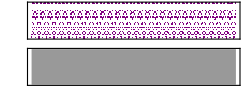

```mathematica
Clear[tonesFormula,s,dataInstrument3,instrument3];
s[n_]:=n^2;
tonesFormula=Table[Mod[s[i],88]-39,{i,1,1200}];
dataInstrument3=Table[{tonesFormula[[i]],1/10,1,1},{i,1,1200}];
instrument3=Sound[{SoundNote[#[[1]],#[[2]],#[[3]],SoundVolume->#[[4]]]&/@dataInstrument3}]
```

Using sequences of digits of famous numbers, Pi

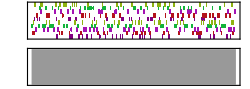

```mathematica
(* create sequences from digits of famous numbers like Pi, E, etc. *)
Clear[bps2,songLength2,x2,sequ2,s2,tones2,rhythm2,instrument2,dataMelody2,melody2];;
bps2=0.05;
songLength2=300;
x2=π;
sequ2=RealDigits[N[x,songLength2]][[1]];
s2[n_]:=sequ2[[n]];
tones2=Table[Mod[s2[i],88]-39,{i,1,songLength2}];
rhythm2=Table[bps2*(Mod[s2[i],4]+1),{i,1,songLength2}];
instrument2=Table[Mod[s2[i],5]+1,{i,1,songLength2}];
volume2=Table[1,{i,1,songLength2}];
dataMelody2=Table[{tones2[[i]],rhythm2[[i]],instrument2[[i]],1},{i,1,songLength2}];
melody2=Sound[{SoundNote[#[[1]],#[[2]],#[[3]],SoundVolume->#[[4]]]&/@dataMelody2}]
```

## References

useful links

Search Engine Google: www.google.com

Online Encyclopedia WIKIPEDIA: www.wikipedia.org

MIDI Manufacturers Association:  www.midi.org

MathSciNet of the American Mathematical Society: www.ams.org

The Mathematical Association of America: www.maa.org

The web's most extensive mathematics resource: mathworld.wolfram.com

Mathematica: www.wolfram.com

MathEverywhere: www.matheverywhere.com

Differential Equations & Mathematica, Carpenter, Davis, Uhl

Dr. Joe Wolfe, Physics Professor at University of New South Wales, Sydney, Australia